# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
(*EnsureFreshKernels[]:=Module[{},
(*Check if the marker variable is defined in any kernel*)If[MemberQ[ParallelEvaluate[$KernelInitializationDone],True],
(*If yes,close and relaunch kernels*)
CloseKernels[];
LaunchKernels[];
];
(*Set or reset the marker variable in all kernels*)
ParallelEvaluate[$KernelInitializationDone=True];]
EnsureFreshKernels[];*)
CloseKernels[];
LaunchKernels[];
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
choiceslist={"Tabulated Nevents+sensitivity","Sensitivity only (tabulated Nevents must be produced before)","Acceptance"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated Nevents+sensitivity"]="Number-of-events+sensitivity";
taglist["Sensitivity only (tabulated Nevents must be produced before)"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

# Preliminary definitions

## Various directories

```mathematica
LLPdirName="Scalar";
(*Set the directory for the search where tabulated acceptances are located*)
directory["Acceptances"]=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
(*Set the directory for the search where tabulated angle-energy distributions are located*)
directory["Distribution"]=FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra",LLPdirName}]; 
(*The directory storing production weights of the given LLP*)
directory["Production weights"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"Production probabilities"}]; 
(*Directory to which various auxillary datasets will be stored*)
directory["Auxiliary"]=FileNameJoin[{NotebookDirectory[],"Auxiliary data",LLPdirName}]; 
If[!DirectoryQ[directory["Auxiliary"]],CreateDirectory[directory["Auxiliary"]]];
(*Directory containing decay widths of the LLPs*)
directory["Decays"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"decay widths"}];
```

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Masses of various SM particles*)
{mSM["Bplus"],mSM["Kplus"],mSM["PiPlus"],mSM["h"],mSM["Bs"]}={5.279,0.495,0.139,62.5,5.366};
(*Fragmentation fractions at the LHC. For the moment, the same fractions are assumed to be at the FCC-hh*)
fbtob0["LHC"]=fbtobplus["LHC"]=fbtob0["FCC-hh"]=fbtobplus["FCC-hh"]=0.324;
fbtobs["LHC"]=fbtobs["FCC-hh"]=0.09;
(*Fragmentation fractions at SPS. From SHiP physics paper*)
fbtobs["SPS"]=0.11;
fbtob0["SPS"]=fbtobplus["SPS"]=0.411;
fstokplus["SPS"]=0.5;
fstok0l["SPS"]=0.25;
(*Fraction of K^(+/-) decaying in-flight at SPS, from https://arxiv.org/pdf/2004.07974.pdf*)
fractionDecayInFlightKplusKminus=(0.29+0.07);
(*Fragmentation fractions at FermilabBD. Assumed to be the same as at SPS*)
fbtobs["FermilabBD"]=0.11;
fbtob0["FermilabBD"]=fbtobplus["FermilabBD"]=0.411;
(*Fragmentation fractions at Serpukhov. Assumed to be zero*)
fbtobs["Serpukhov"]=0.;
fbtob0["Serpukhov"]=fbtobplus["Serpukhov"]=0.;

(*Fragmentation fractions at LHC fixed target*)
(*Calculated for c quarks and estimated for b quarks*)
fbtobplus["LHC-fixed-target"]=0.4;
fbtob0["LHC-fixed-target"]=0.4;
fbtobs["LHC-fixed-target"]=0.1; 
(*copied for SPS*)
fstokplus["LHC-fixed-target"]=0.5;
fstok0l["LHC-fixed-target"]=0.25;
```

## LLP phenomenology: prodution probabilities, decay widths

## Scanning for tabulated distributions

```mathematica
(*Define the file pattern*)
pattern="DoubleDistr_*_*_*.m";
(*Search for files matching the pattern in the directory and its subdirectories*)
matchingFiles=FileNames[pattern,{directory["Distribution"]},Infinity];
(*List of LLPs, production modes, and facilities for which the tabulated distributions have been computed at the previous stage of using SensCalc*)
ExtractedProductionParameters=Function[filename,parts=StringSplit[FileNameTake[filename],"_"];
{parts[[2]],parts[[3]],StringDrop[parts[[4]],-2]} ];
(*combinations selected LLP, production channel, facility for which the tabulated distributions are present*)
DistrCombinations=(ExtractedProductionParameters/@matchingFiles)//Sort;
```

## Production weights

```mathematica
FacilitiesList={"SPS","FermilabBD","LHC","FCC-hh","Serpukhov", "LHC-fixed-target"};
intProd[filename_,m1_,m2_]:=If[mLLP<m1-m2,Evaluate[Interpolation[Import[FileNameJoin[{directory["Production weights"],filename}],"Table"],InterpolationOrder->1][mLLP]],0.];
BrhtoSS[mLLP_,α_]=2*10^-2*α^2 √(1-4*mLLP^2/125^2);
(*Value of α corresponding to the given Br(h->SS)=0.01*)
αvalBrhToSS[mS_,BrhToSS_]=α/.Solve[BrhtoSS[mS,α]==BrhToSS,α][[2]];
Print["Exclusive/inclusive production of dark scalar in decays B->X_s+S"]
SelectedBrChoice=dropdownDialog[{"Exclusive","Inclusive"},"Select the description of the scalar's production by decays of B via mixing (see 1904.10447):"]
Do[
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"B-mixing",Facility]=θ2*(fbtob0[Facility]+fbtobplus[Facility])intProd[If[SelectedBrChoice=="Exclusive","BtoXsStotal.dat","BtoXsSinclusive.dat"],mSM["Bplus"],mSM["PiPlus"]];
(*Factors of 2 and 1/2 are due to the production of scalars in pairs. α is the quartic coupling defined by Subscript[L, int] = α/(2v)S^2 H^+H*)
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"B-quartic",Facility]=2*αvalBrhToSS[mLLP,BrhToSS]^2*(fbtob0[Facility]+fbtobplus[Facility])*intProd["BplustoXsSStotal.dat",mSM["Bplus"]/2,mSM["PiPlus"]/2];
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"Bs-quartic",Facility]=2*αvalBrhToSS[mLLP,BrhToSS]^2*fbtobs[Facility]*intProd["BstoSS.dat",mSM["Bs"]/2,0.];
If[MemberQ[{"LHC","FCC-hh"},Facility],
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"h-quartic",Facility]=2*10^-2*αvalBrhToSS[mLLP,BrhToSS]^2 √(1-4*mLLP^2/125^2);
];
,{Facility,FacilitiesList}];
(*________________*)
(*Bremsstrahlung*)
(*________________*)
bremfacilities=Select[DistrCombinations,#[[2]]=="Bremsstrahlung-mixing"&][[All,3]];
Print[bremfacilities]
BremProd[Facility_]:=Module[{},
If[MemberQ[bremfacilities,Facility],
datbrem[mLLP_,θLLP_]=Import[FileNameJoin[{directory["Production weights"],"Pbrem_"<>LLPdirName<>"_"<>Facility<>".m"}],"MX"];
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"Bremsstrahlung-mixing",Facility]=datbrem[mLLP,θLLP][[1]]*θ2;
ELLPmin["Bremsstrahlung-mixing",Facility]=Evaluate[datbrem[mLLP,θLLP][[2]]];
ELLPmax[mLLP_,θLLP_,"Bremsstrahlung-mixing",Facility]=Evaluate[datbrem[mLLP,θLLP][[3]]]
]
]
Do[
BremProd[Facility],{Facility,FacilitiesList}]
(*Production from K at beam dump experiments with thick target. Assumed to be the same independently of target's material. Also, the fraction of Subscript[(K^0), L] decaying at rest is assumed to be the same as the fraction of charged kaons*)
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"K-mixing","SPS"]=
θ2*(fstokplus["SPS"]*intProd["KplustoPiS.dat",mSM["Kplus"],mSM["PiPlus"]]+fstok0l["SPS"]*intProd["K0LtoPiS.dat",mSM["Kplus"],mSM["PiPlus"]]);
(*For LHC-fixed-target same procedure as for SPS*)
PmotherToLLP[mLLP_,θ2_,BrhToSS_,"K-mixing","LHC-fixed-target"]=
θ2*(fstokplus["LHC-fixed-target"]*intProd["KplustoPiS.dat",mSM["Kplus"],mSM["PiPlus"]]+fstok0l["LHC-fixed-target"]*intProd["K0LtoPiS.dat",mSM["Kplus"],mSM["PiPlus"]]);

WeightsCombinations=Cases[Keys[DownValues@PmotherToLLP][[All,1,#]]&/@{4,5}//Transpose//Sort,_?(MemberQ[DistrCombinations[[All,{2,3}]],#]&)];
Print[Keys[DownValues@PmotherToLLP][[All,1,#]]&/@{4,5}//Transpose//Sort]
Print[DistrCombinations[[All,{2,3}]]]
Print[WeightsCombinations]

Print["If there are production weights to all available distributions:"]
IfCondDistrToWeights=DistrCombinations[[All,{2,3}]]==WeightsCombinations
If[!IfCondDistrToWeights,Module[{missingCombinations},
(*Identify missing combinations*)
missingCombinations=Complement[DistrCombinations[[All,{2,3}]],WeightsCombinations];
(*Print a message if there are missing combinations*)
If[missingCombinations=!={},Print["The following required combinations are missing from the provided weights:"];
Print[missingCombinations];];];
(*Show an info dialog*)
infoDialog["You have not provided the production probabilities PmotherToLLP to all the generated tabulated distributions! Please do this first to avoid problems"];];

(*Scaling of the lower bound: Subscript[(θ^2), lower bound] ~ (Subscript[N, ev]|_(θ = 1))^(-β/2)*)
LowerBoundScaling["B-mixing"]=LowerBoundScaling["Bremsstrahlung-mixing"]=LowerBoundScaling["K-mixing"]=1;
LowerBoundScaling["B-quartic"]=LowerBoundScaling["Bs-quartic"]=LowerBoundScaling["h-quartic"]=2;
```

## Scalar lifetime and branching ratios

### Lifetimes

```mathematica
(*Decay length of the scalar - following Winkler*)
cτLLP[mLLP_,θ2_]=1/θ2 Interpolation[Select[Import[FileNameJoin[{directory["Decays"],"ctaus.dat"}],"Table"],#[[1]]≠2.&],InterpolationOrder->1][mLLP];
ldecayLLP[mLLP_,θ2_,ELLP_]=cτLLP[mLLP,θ2]*(√(ELLP^2-mLLP^2))/mLLP;
```

## Loading necessary routines

```mathematica
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/generic.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/for-sensitivities.nb"}]];
inecessary={1,2,3};
]
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
ExperimentDirectoriesList=Select[FileNames["*",directory["Acceptances"],1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{directory["Acceptances"],ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_``.m",ExperimentsListTemp[[i]],LLPdirName]}]},{i,1,Length[ExperimentsListTemp]}],2];
Print["List of available experiments:"]
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events+sensitivity",
Do[
BlockEvaluation["Number-of-events-computation+sensitivity"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

# Number of events

## Particular experiment

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
```

## Cross-sections, acceptances

## Cross-sections, acceptances

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{directory["Acceptances"],SelectedExperiment,ToString@StringForm["Acceptance_``_for_``.m",Sequence@@{SelectedExperiment,LLPdirName}]}]}],"MX"];//AbsoluteTiming
{FacilityGivenExperiment,FullAcceptanceData0,BrVis[mLLP_]}=dataAcceptances[[#]]&/@{1,3,5};
LogLogPlot[Evaluate[BrVis[mLLP]],{mLLP,0.02,10},Frame->True,ImageSize->Large,FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{{0.1,10},{0.01,1.2}},Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment}], 20, Black]]
(*___________________________*)
(*Interpolation of the tabulated azimuthal acceptance, extracting Subscript[θ, min/max], etc.*)
(*___________________________*)
{AzimuthalAcceptanceInt[θLLP_,zLLP_],θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp,zminθ[θLLP_],zmaxθ[θLLP_]}=BlockϵAzimuthal[FullAcceptanceData0];
(*Logarithmized data with full acceptance, and also decay acceptance and full acceptance interpolations*)
{FullAcceptanceData,DecayAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],FullAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,ϵvals,ϵazvals,mminϵ,mmaxϵ}=BlockϵDecay[FullAcceptanceData0,zminExp,BrVis];
CrossSectionData=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="Npot"&][[1]][[2]]//N;
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
(*Total number of b b̄ and h*)
ProbMother["B-mixing"]=ProbMother["B-quartic"]=ProbMother["Bs-quartic"]=Select[CrossSectionData,#[[1]]=="Pb"&][[1]][[2]];
ProbMother["h-quartic"]=Select[CrossSectionData,#[[1]]=="Ph"&][[1]][[2]];
ProbMother["K-mixing"]=If[FacilityGivenExperiment=="SPS" ||FacilityGivenExperiment=="LHC-fixed-target",fractionDecayInFlightKplusKminus,0.];
ProbMother["Bremsstrahlung-mixing"]=1.;
{{"χ_(b  or  OverscriptBox[b, _])","χ_h"},{ProbMother["B-mixing"],ProbMother["h-quartic"]}}//TableForm
Row[{"Search for "<>LLPdirName<>" at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

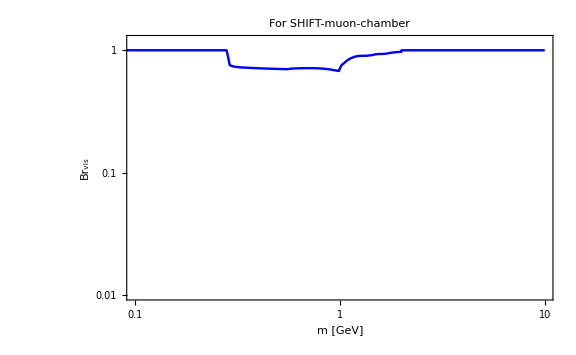

## LLP angle-energy distributions for the given experiment

```mathematica
ProductionPatternSelected=Select[DistrCombinations,#[[3]]==FacilityGivenExperiment&];
Print["Production list:"]
ELLPmax[mLLP_,θLLP_,"Bremsstrahlung-mixing"]=ELLPmax[mLLP,θLLP,"Bremsstrahlung-mixing",FacilityGivenExperiment];
ELLPmin["Bremsstrahlung-mixing"]=ELLPmin["Bremsstrahlung-mixing",FacilityGivenExperiment];
ProductionListTemp=ProductionPatternSelected[[All,2]]//DeleteDuplicates;
ProductionList=If[ELLPmin["Bremsstrahlung-mixing"]<ELLPmax[0.02,θminExp,"Bremsstrahlung-mixing"],ProductionListTemp,Select[ProductionListTemp,#!="Bremsstrahlung-mixing"&]]
θmaxBrem=Abs[θLLP/.Solve[ELLPmax[0.02,θLLP,"Bremsstrahlung-mixing"][[2]]==ELLPmin["Bremsstrahlung-mixing"],θLLP][[1]]];
Do[
Module[{prod},
prod=ProductionPatternSelected[[i]][[2]];
(*Importing the data with distribution*)
dirimp=If[prod=="DrellYan",FileNameJoin[{directory["Distribution"],"Pregenerated"}],directory["Distribution"]];
DistrDataImport[prod]=Import[FileNameJoin[{dirimp,"DoubleDistr_"<>LLPdirName<>"_"<>prod<>"_"<>FacilityGivenExperiment<>".m"}],"MX"];
(*Min/mass mass of the LLP from the data*)
mlistDistr[prod]=DeleteDuplicates[DistrDataImport[prod][[All,1]]];
{mLLPmin[prod],mLLPmax[prod]}=MinMax[mlistDistr[prod]];
(*Interpolation of the tabulated distribution*)
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=10^(Interpolation[distrlogComp[DistrDataImport[prod]],InterpolationOrder->1][Log10[mLLP],Log10[θLLP],Log10[ELLP]]);
If[prod=="Bremsstrahlung-mixing",
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=If[ELLP<=ELLPmax[mLLP,θLLP,"Bremsstrahlung-mixing"],Evaluate[DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0.]];
(*Probability to produce LLP*)
ProbLLP[mLLP_,θ2_,BrhToSS_,prod]=ProbMother[prod]*PmotherToLLP[mLLP,θ2,BrhToSS,prod,FacilityGivenExperiment];
]
,{i,1,Length[ProductionPatternSelected],1}]
```

## Importing and interpolating

```mathematica
ProductionPatternSelected=Select[DistrCombinations,#[[3]]==FacilityGivenExperiment&];
Print["Production list:"]
ELLPmax[mLLP_,θLLP_,"Bremsstrahlung-mixing"]=ELLPmax[mLLP,θLLP,"Bremsstrahlung-mixing",FacilityGivenExperiment];
ELLPmin["Bremsstrahlung-mixing"]=ELLPmin["Bremsstrahlung-mixing",FacilityGivenExperiment];
ProductionListTemp=ProductionPatternSelected[[All,2]]//DeleteDuplicates;
ProductionList=If[ELLPmin["Bremsstrahlung-mixing"]<ELLPmax[0.02,θminExp,"Bremsstrahlung-mixing"],ProductionListTemp,Select[ProductionListTemp,#!="Bremsstrahlung-mixing"&]]
θmaxBrem=Abs[θLLP/.Solve[ELLPmax[0.02,θLLP,"Bremsstrahlung-mixing"][[2]]==ELLPmin["Bremsstrahlung-mixing"],θLLP][[1]]];
Do[
Module[{prod},
prod=ProductionPatternSelected[[i]][[2]];
(*Importing the data with distribution*)
dirimp=If[prod=="DrellYan",FileNameJoin[{directory["Distribution"],"Pregenerated"}],directory["Distribution"]];
DistrDataImport[prod]=Import[FileNameJoin[{dirimp,"DoubleDistr_"<>LLPdirName<>"_"<>prod<>"_"<>FacilityGivenExperiment<>".m"}],"MX"];
(*Min/mass mass of the LLP from the data*)
mlistDistr[prod]=DeleteDuplicates[DistrDataImport[prod][[All,1]]];
{mLLPmin[prod],mLLPmax[prod]}=MinMax[mlistDistr[prod]];
(*Interpolation of the tabulated distribution*)
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=10^(Interpolation[distrlogComp[DistrDataImport[prod]],InterpolationOrder->1][Log10[mLLP],Log10[θLLP],Log10[ELLP]]);
If[prod=="Bremsstrahlung-mixing",
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=If[ELLP<=ELLPmax[mLLP,θLLP,"Bremsstrahlung-mixing"],Evaluate[DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0.]];
(*Probability to produce LLP*)
ProbLLP[mLLP_,θ2_,BrhToSS_,prod]=ProbMother[prod]*PmotherToLLP[mLLP,θ2,BrhToSS,prod,FacilityGivenExperiment];
]
,{i,1,Length[ProductionPatternSelected],1}]
directory["Auxiliary-experiment"]=FileNameJoin[{directory["Auxiliary"],SelectedExperiment}];
If[!DirectoryQ[directory["Auxiliary-experiment"]],CreateDirectory[directory["Auxiliary-experiment"]]];
Export[FileNameJoin[{directory["Auxiliary-experiment"],"Double-Distr-Averaged-"<>LLPdirName<>".m"}],{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],1/Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}] Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]*DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0],{prod,ProductionList}]},"MX"];
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod,DistrDataImport],{prod,ProductionList}];//AbsoluteTiming
(*____________________________*)
(*Finding Subscript[E, max](Subscript[m, LLP],Subscript[θ, LLP]) for the angular range at the given experiment*)
(*____________________________*)
Do[ELLPmax[mfip_,θfip_,prod]=EmaxBlock[prod,8,DistrDataImport,FacilityGivenExperiment],{prod,Select[ProductionList,#!="Bremsstrahlung-mixing"&]}]//AbsoluteTiming
ptenergies=LogLogPlot[Evaluate[Table[ELLPmax[0.1,θLLP,prod],{prod,ProductionList}]],{θLLP,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
ptprodprob=LogLogPlot[Evaluate[Table[ProbLLP[ma,1,0.01,prod],{prod,ProductionList}]],{ma,mminϵ,mmaxϵ},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
Style[Row[{ptprodprob,ptenergies}],ImageSizeMultipliers->{1, 1}]
```

## Number of events

## Number of events

### Initializing all routines

```mathematica
Do[{OutGridθfinal[prod],Δθvals[prod]}=OutGridθTemp[InGridθϵ,30,prod,θmaxBrem],{prod,ProductionList}]
{OutGridzfinal,Δzvals}=OutGridszTemp[InGridzϵ,30,zminExp];
(*Final energy grid. Mass- and production channel-dependent*)
If[FacilityGivenExperiment!="ESS",
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<=400},{25,400<Efip<600},{50,600<=Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
emin=If[ProdChannel!="Bremsstrahlung-mixing",N[m],ELLPmin["Bremsstrahlung-mixing"]];
egridtemp=With[{start=emin,end=ELLPmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N;
If[Length[egridtemp]==1,egridtemp=Join[egridtemp,{Log10[2*emin]}]];
egridtemp
]
,
StepEtemp[Efip_]=0.001;
OutGridEnergy[m_,ProdChannel_]:=Block[{},
tabt=Table[e,{e,1.0001m,ELLPmax[m,θminExp,ProdChannel],0.001}];
If[Length[tabt]==1,tabt=Join[tabt,{ELLPmax[m,θminExp,ProdChannel]}]//Sort//DeleteDuplicates];
Log10[tabt]//N
]
]
(*____________________________________________________*)
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
(*____________________________________________________*)
(*The block which sets all the values of Subscript[ϵ, Full]×Subscript[f, θ,E] for which E < Subscript[E, max] to zero, for Bremsstrahlung*)
emaxbrem[mLLP_,θLLP_]=ELLPmax[mLLP,θLLP,"Bremsstrahlung-mixing"];
BremCutComp=Hold@Compile[{{angleenergy,_Real,1},{mfip,_Real}},Module[{angles,energies,distrvals,d},
angles=Compile`GetElement[angleenergy,1];
energies=Compile`GetElement[angleenergy,2];
distrvals=Compile`GetElement[angleenergy,3];
d=If[energies<emaxbrem[mfip,angles],distrvals,10^-90.];
d
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.DownValues@emaxbrem//ReleaseHold;
BremCut[OutGridθfinal_,OutGridEfinal_,distr_,mLLP_]:=Block[{},
angleenergy=Join[10^Tuples[{OutGridθfinal,OutGridEfinal}],Partition[distr,1],2];
BremCutComp[angleenergy,mLLP]
]
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=TableIntegrandDiscretTemp[m,ProdChannel,ϵDecOp,ϵvals,ϵazvals,OutGridθfinal[ProdChannel],OutGridzfinal,OutGridEnergy,InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,Δθvals[ProdChannel],Δzvals,zminExp,GridInFinal,DistrVals,FacilityGivenExperiment]
```

### Generalized acceptances

```mathematica
(*Tabulated acceptance*)
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=AcceptanceDiscretTemp[m,ProdChannel,ϵdecOp,decProb,mLLPmin,mminϵ,mLLPmax,mmaxϵ,ELLPmax,θminExp,TableIntegrandDiscret,BrVis,zmaxExp,zminExp,FactorANUBISceiling,0.]
Do[mlistAcceptance[prod]=Select[Join[{1.01Max[mLLPmin[prod],mminϵ]},10^InGridmϵ,{Min[mLLPmax[prod],mmaxϵ]}],mLLPmin[prod]<=#<=mLLPmax[prod]&]//Sort//DeleteDuplicates;
,{prod,ProductionList}];
Do[
ϵGeomTabs[prod]=ParallelTable[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}];
,{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[Evaluate[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]}],FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{Max[0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],10^-5],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_LLP>","<ϵ_LLPϵ_decay>","cτ<ϵ_LLPP_decay>","cτ<ϵ_LLPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
(*Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-fermion_at_``_From_``.dat",Sequence@@{SelectedExperiment,ExportList[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]*)
AccAveraged[mLLP_,θ2_,BrhToSS_]=NpotGivenExperiment{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,θ2,BrhToSS,prod]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,θ2,BrhToSS,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,θ2,BrhToSS,prod]/cτacc*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,θ2,BrhToSS,prod]/cτacc*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}]};
Export[FileNameJoin[{directory["Auxiliary-experiment"],"AcceptanceAveraged-"<>LLPdirName<>".m"}],AccAveraged[mLLP,θ2,BrhToSS],"MX"];
```

### Rough estimates of the upper and lower bounds

#### Definitions

```mathematica
BrhToSSreference=0.15;
Do[
factorLowerBound=If[StringContainsQ[prod,"mixing"],1/2,1];
LowerBoundEstimate[mLLP_,prod]=((NpotGivenExperiment*ProbLLP[mLLP,1,BrhToSSreference,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP])/(2.3ldecayLLP[mLLP,1,ELLP] mLLP/(√(ELLP^2-mLLP^2))))^-factorLowerBound;
UpperBoundEstimate[mLLP_,prod]=(Abs[Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*ProbLLP[mLLP,1,BrhToSSreference,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mLLP],b->zminExp/ldecayLLP[mLLP,1,ELLPmax[0.5,θminExp,prod]]}]]]),{prod,ProductionList}]
ProdTest=ProductionList[[2]]
LogLogPlot[Evaluate[{0.3LowerBoundEstimate[mLLP,ProdTest],1.8UpperBoundEstimate[mLLP,ProdTest]}],{mLLP,Max[mLLPmin[ProdTest],mminϵ],Min[mLLPmax[ProdTest],mmaxϵ]},Frame->True,ImageSize->Large]
```

### Number of events - fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,BrhToSS_,θ2list_]:=Module[{NevDiscret(*,NpotTimesχval*)},
If[Max[mminϵ,mLLPmin[ProdChannel]]<m<Min[mLLPmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[θ2_]=FactorANUBISceiling*NpotGivenExperiment*ProbLLP[m,θ2,BrhToSS,ProdChannel];
{lowerbound,upperbound}={LowerBoundEstimate[m,ProdChannel],UpperBoundEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[θ2_]:=If[brvis!=0,If[FactorLowerBound*lowerbound<θ2<2upperbound,NpotTimesχval[θ2]*brvis*sumcompile[tableprefac[integrandtab,m,cτLLP[m,θ2],1,0.]],0.],0.];
Table[{m,θ2list[[i]],NevDiscret[θ2list[[i]]]},{i,1,Length[θ2list],1}],Table[{m,θ2list[[i]],0.},{i,1,Length[θ2list],1}]]
]
```

```mathematica
distrevents[0.5,0.015,10,100*10^-12.,0.5]
```

```mathematica
0.1/(100*10^-12.)
```

```mathematica
distrevents[m_,θ_,ES_,cτ_,l_]=DoubleDistrLLPint[m,θ,ES,"B-mixing"]Exp[-l/(cτ*(√(ES^2-m^2))/m)];
distr[m_,cτ_]:=ParallelTable[{l,Quiet[NIntegrate[distrevents[m,Exp[th],Exp[es],cτ,l]Exp[th+es],{th,Log[0.013],Log[0.26]},{es,Log[m],Log[5000]},Method->"AdaptiveMonteCarlo"]]},{l,0.1,300,0.3}]
d1=distr[0.5,500*10^-12*3*10^8];
d2=distr[2.5,500*10^-12*3*10^8];
d3=distr[0.5,100*10^-12*3*10^8];
```

```mathematica
d3=distr[0.5,100*10^-12*3*10^8];
```

```mathematica
lmean[data_]:=Block[{},
lint[x_]=Exp[Interpolation[Log[data],InterpolationOrder->1][Log[x]]];
NIntegrate[lint[x]*x,{x,data[[All,1]]//Min,data[[All,1]]//Max}]/NIntegrate[lint[x],{x,data[[All,1]]//Min,data[[All,1]]//Max}]
]
lmean[d1]
lmean[d2]
lmean[d3]
ListLogLogPlot[{d1,d2,d3},ImageSize->Large,Frame->True,Joined->True]
lmean1[data_]:=Block[{},
lint[x_]=Exp[Interpolation[Log[data],InterpolationOrder->1][Log[x]]];
NIntegrate[lint[x]*x,{x,data[[All,1]]//Min,16.}]/NIntegrate[lint[x],{x,data[[All,1]]//Min,16.}]
]
lmean1[d1]
lmean1[d2]
lmean1[d3]
```

### Number of events - slow (using built-in Mathematica functions Interpolation, NIntegrate)

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mLLP_,coupling_,θLLP_,ELLP_,zLLP_]=Exp[-zLLP/(Cos[θLLP]*ldecayLLP[mLLP,coupling,ELLP])]/(Abs[Cos[θLLP]]*ldecayLLP[mLLP,coupling,ELLP]);
(*The integrand determining the differential rate for events*)
Do[IntegrandLLP[mLLP_,coupling_,θLLP_,ELLP_,zLLP_,prod]=DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]*PdecayDensity[mLLP,coupling,θLLP,ELLP,zLLP]*AzimuthalAcceptanceInt[θLLP,zLLP]*DecayAcceptanceInt[mLLP,θLLP,ELLP,zLLP],{prod,ProductionList}]
IntegralLLP[mLLP_,coupling_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,Exp[ELLP],zLLP,ProdChannel]Exp[ELLP]],{θLLP,θminExp,θmaxExp},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,θLLP,ProdChannel]]},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
(*IntegralLLP[mLLP_,finv_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,finv,Exp[θLLP],Exp[ELLP],Exp[zLLP],ProdChannel]]Exp[θLLP+ELLP+zLLP],{θLLP,Log[θminExp],Log[θmaxExp]},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,Exp[θLLP],ProdChannel]]},{zLLP,Log[zminθ[Exp[θLLP]]],Log[zmaxθ[Exp[θLLP]]]},Method->"AdaptiveMonteCarlo"]*)
NeventsInt[mLLP_,θ2_,BrhToSS_,ProdChannel_]:=FactorANUBISceiling*If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0,If[FactorLowerBound*LowerBoundEstimate[mLLP,ProdChannel]<θ2<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,θ2,BrhToSS,ProdChannel]*IntegralLLP[mLLP,θ2,ProdChannel],0.],0.]
IntegralLLPE[mLLP_,θ2_,ProdChannel_,ELLP_]:=NIntegrate[Abs[IntegrandLLP[mLLP,θ2,θLLP,ELLP,zLLP,ProdChannel]],{θLLP,θminExp,θmaxExp},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
NeventsDiffIntE[mLLP_,θ2_,BrhToSS_,ProdChannel_,ELLP_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0&&mLLP<ELLP<=ELLPmax[mLLP,θminExp,ProdChannel],If[0.1LowerBoundEstimate[mLLP,ProdChannel]<θ2<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,θ2,BrhToSS,ProdChannel]*IntegralLLPE[mLLP,θ2,ProdChannel,ELLP],0.],0.]
IntegralLLPz[mLLP_,θ2_,ProdChannel_,zLLP_]:=NIntegrate[Abs[IntegrandLLP[mLLP,θ2,θLLP,Exp[ELLP],zLLP,ProdChannel]]Exp[ELLP],{θLLP,θminExp,θmaxExp},{ELLP,Log[mLLP],Log[Evaluate[ELLPmax[mLLP,θLLP,ProdChannel]]]},Method->"AdaptiveMonteCarlo"]
NeventsDiffIntz[mLLP_,θ2_,BrhToSS_,ProdChannel_,zLLP_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0&&zminExp<=zLLP<=zmaxExp,If[0.1LowerBoundEstimate[mLLP,ProdChannel]<θ2<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,θ2,BrhToSS,ProdChannel]*IntegralLLPz[mLLP,θ2,ProdChannel,zLLP],0.],0.]
```

## Tests

### Total number of events

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
(*A separate discussion should be made for the couplings belong to the domain cτ γ << Subscript[z, experiment]. The discrepancy may be significant, and the reason is insufficient grid density for the fast integration method. However, due to the exponential suppression of the number of events, this may be compensated by a tiny shift in the coupling, so the discrepancy should be considered as appropriate.*)
mtest=If[MemberQ[{"LHC","FCC-hh"},FacilityGivenExperiment]==True,5,0.5];
ProdTest=If[MemberQ[{"LHC","FCC-hh"},FacilityGivenExperiment]==True,"h-quartic","B-mixing"];
couplinglist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-17.,-3.,0.3}];
dat1=NeventsDiscret[mtest,ProdTest,BrhToSSreference,couplinglist];//AbsoluteTiming
dat2=ParallelTable[{couplinglist[[i]],cτLLP[mtest,couplinglist[[i]]],Quiet[NeventsInt[mtest,couplinglist[[i]],BrhToSSreference,ProdTest]]},{i,1,Length[couplinglist],1}];//AbsoluteTiming
Join[{{"m_LLP/GeV","coupling","cτ/z_min","N_(events, fast)","N_(events, slow)"}},Join[dat1[[All,{1,2}]],{(#[[2]])/zminExp}&/@dat2,dat1[[All,{3}]],dat2[[All,{3}]],2]]//TableForm
```

### Differential number of events

```mathematica
(*Variable = "E_X","z_X","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"z_X"->3}]
Do[
Δxvals["E_X",prod]:=ΔEvals;
Δxvals["z_X",prod]=Δzvals;
Δxvals["θ_X",prod]=Δθvals[prod]
,{prod,ProductionList}];
LegendX:=Association[{"E_X"->"E_X [GeV]","θ_X"->"θ_X [rad]","z_X"-> "z_X [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_X [GeV^-1]","θ_X"->"dN_ev/dθ_X [rad^-1]","z_X"-> "dN_ev/dz_X [m^-1]"}]
(*Differential number of events*)
NeventsDifferentialDiscretProd[m_,ProdChannel_,coupling_,BrhToSS_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*ProbLLP[m,coupling,BrhToSS,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
OutGridEfinalTemp=OutGridEnergy[N[m],ProdChannel];
ΔEvals=(Rest[10^OutGridEfinalTemp]-Most[10^OutGridEfinalTemp]);
Δxval=Δxvals[Variable,ProdChannel];
cτVal=cτLLP[m,coupling];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal,0.],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
NeventsDifferentialDiscret[m_,coupling_,BrhToSS_,Variable_]:=Module[{NdiffInt,LegendList,QuantityMinMax,ValueMinMax},
prodlisttemp={};
Do[If[Max[mLLPmin[prod],mminϵ]<m<Min[mLLPmax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscretProd[m,prod,coupling,BrhToSS,Variable];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax;
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
{Table[NdiffInt[X,prod],{prod,LegendList}],LegendList,QuantityMinMax,ValueMinMax}
]
mvaltest=If[FacilityGivenExperiment=="ESS",0.04,3];
couplingvaltest=1.4LowerBoundEstimate[mvaltest,"B-mixing"];
BrhToSStest=0.0;
quantity="θ_X";
{NdiffTab[X_],LegendList,QuantityMinMax,ValueMinMax}=NeventsDifferentialDiscret[mvaltest,couplingvaltest,BrhToSStest,quantity];
Do[
prch=LegendList[[i]];
NdiffInt[X_,prch]=NdiffTab[X][[i]];
,{i,1,Length[LegendList]}];
plotdiff=LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,Right],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 18],PlotLabel->Style[Row[{SelectedExperiment,". m_S = ",mvaltest," GeV, θ^2 = ",couplingvaltest//N,", Br_(h -> SS) = ",BrhToSStest}],14,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
directory["Nevents"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}];
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
directory["Nevents-LLP-experiment"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName,SelectedExperiment}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Nevents","Nevents-LLP","Nevents-LLP-experiment"};
Print["Filenames with tabulated N_events:"]
Do[FilenameNeventsInt[prod]=ToString@StringForm["Nevents_``_``_at_``_Npot=``.dat",Sequence@@{LLPdirName,prod,SelectedExperiment,NpotGivenExperiment//CForm//ToString}],{prod,ProductionList}]
FilenameNeventsInt[#]&/@ProductionList
mRangeExport["Bremsstrahlung-mixing"]={0.021,0.051,0.1,0.13,0.15,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.225,0.23,0.24,0.25,0.26,0.27,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,1.99,2.1,2.2,2.3,2.4,2.5};
mRangeExport["K-mixing"]={0.021,0.051,0.1,0.13,0.15,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.23,0.24,0.25,0.26,0.27,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.995(mSM["Kplus"]-mSM["PiPlus"])};
mRangeExport["B-quartic"]={0.021,0.051,0.1,0.13,0.15,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.23,0.24,0.25,0.26,0.27,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,1.99,2.05,2.1,2.2,2.3,2.4,2.5,2.55};
mRangeExport["B-mixing"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.23,0.24,0.25,0.26,0.27,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,1.99,2.1,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3,3.1,3.2,3.3,3.5,3.6,3.7,3.8,3.9,4,4.1,4.2,4.3,4.4,4.5,4.6,4.65,4.7,4.75,4.77,4.8,4.83,4.85,4.87,4.9,4.93,4.95,4.97,5,5.03,5.05,5.07,5.1};
mRangeExport["Bs-quartic"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.23,0.25,0.26,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.5,0.55,0.6,0.65,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,1.99,2.05,2.1,2.2,2.3,2.4,2.5,2.55,2.6,2.65};
mRangeExport["h-quartic"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.205,0.21,0.212,0.214,0.216,0.218,0.22,0.23,0.24,0.25,0.26,0.27,0.275,0.28,0.285,0.289,0.3,0.32,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,1.99,2.1,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5,5.1,7.,10.,10.6,12.,15.,20.,30.,40.,45.,50.,55.,60.,61.,62.,62.49};
couplingsRangeExport=Table[10^x,{x,-20,-3,0.02}]//N;
```

## Exporting

```mathematica
BlockExport[ProdChannel_]:=Block[{},
mlist=mRangeExport[ProdChannel];
TabFrom=ParallelTable[Quiet[NeventsDiscret[mlist[[k]],ProdChannel,BrhToSSreference,couplingsRangeExport]],{k,1,Length[mlist],1}];
Export[FileNameJoin[{directory["Nevents-LLP-experiment"],FilenameNeventsInt[ProdChannel]}],Flatten[TabFrom,1],"Table"]
]
Monitor[
Do[
prod=ProductionList[[j]];
BlockExport[prod],{j,1,Length[ProductionList],1}],
Row[{ProgressIndicator[j,{1,Length[ProductionList]}]," Production mode = ",ProductionList[[j]]," (", j,"/",Length[ProductionList],")"}]]//AbsoluteTiming
If[icounter>Length[SelectedExperimentList],BlockEvaluation["Sensitivity"]]
```

# Computing sensitivities

## Basic definitions

```mathematica
BrhToSSreference=0.15;
LLPdirName="Scalar";
directory["Sensitivity"]=FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}];
directory["Sensitivity-LLP"]=FileNameJoin[{directory["Sensitivity"],LLPdirName}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Sensitivity","Sensitivity-LLP"};
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ExperimentDirectoriesListNevents=Select[FileNames["*",directory["Nevents-LLP"],1],DirectoryQ];
Print["List of available experiments with tabulated N_events for " <>LLPdirName<>":"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"],
SelectedExperimentList=If[Length[ExperimentsListNevents]≠0,selectionDialog[ExperimentsListNevents,"Select the experiments for which the sensitivity will be computed:"]];
icounter=1;
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
];
Do[
BlockEvaluation["Sensitivity-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
```

## Importing data and interpolations

## Selecting experiment

```mathematica
Print["Selected experiment:"]
GivenExperimentForSensitivityComputation=SelectedExperimentList[[icounter++]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
PathsNeventsSelected={};
Do[PathsNeventsSelected=Join[PathsNeventsSelected,FileNames["*.dat",FileNameJoin[{directory["Nevents-LLP"],exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
(*Filenames=Table[{StringReplace[Last@FileNameSplit@files[[i]],{"e+0":>"*^","e-0":>"*^-"}]},{i,1,Length[files],1}];*)
(*Creating the directory for exporting sensitivity curves*)
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
directory["Sensitivity-LLP-exp"]=FileNameJoin[{directory["Sensitivity-LLP"],ExperimentFolder}];
If[!DirectoryQ[directory["Sensitivity-LLP-exp"]],CreateDirectory[directory["Sensitivity-LLP-exp"]]]
```

## Importing and interpolations

```mathematica
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@PathsNeventsSelected[[i]],{i,1,Length[PathsNeventsSelected],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_Scalar_"~~mother__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~".dat":>{mother,experiment,Npot}][[1]]
(*______________________________________________________*)
(*Importing and interpolation*)
(*______________________________________________________*)
ProductionInfoList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
Join[{{"Mother","Experiment","N_PoT"}},ProductionInfoList]//TableForm
ProductionChannelsList=ProductionInfoList[[All,1]];
NpotDefault=Interpreter["Number"][ProductionInfoList[[1]][[3]]];
NeventsTabulated//Clear;
ϵreco[mLLP_]=If[StringContainsQ[GivenExperimentForSensitivityComputation,"LHCb-downstream"]==True,0.4,If[StringContainsQ[GivenExperimentForSensitivityComputation,"CHARM-lepton"]==True,If[mLLP<0.105*2,0.51,0.85],1]];
Do[
Module[{prod},
prod=ProductionChannelsList[[i]];
(*The condition if one sums the number of events for the same production mode over several experiments*)
IfprodExists=MemberQ[Keys[DownValues@NeventsTabulated][[All,1,1]],prod];
NeventsTabulated[prod]=If[!IfprodExists,Import[PathsNeventsSelected[[i]],"Table"],Join[NeventsTabulated[prod][[All,{1,2}]],NeventsTabulated[prod][[All,{3}]]+Import[PathsNeventsSelected[[i]],"Table"][[All,{3}]]]];
{mminmax[prod],couplingminmax[prod]}=(NeventsTabulated[prod][[All,#]]//MinMax)&/@{1,2};
NevMax[prod]=NeventsTabulated[prod][[All,3]]//Max;
NevInt[mLLP_,θ2_,BrhToSS_,prod]=If[StringContainsQ[prod,"quartic"],BrhToSS/BrhToSSreference,1]*ϵreco[mLLP]*If[mminmax[prod][[1]]≤ mLLP≤mminmax[prod][[2]]&&couplingminmax[prod][[1]]≤θ2≤couplingminmax[prod][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulated[prod],InterpolationOrder->1][Log10[mLLP],Log10[θ2]])],0];
]
,{i,1,Length[ProductionInfoList],1}]
{mminmaxOverall,couplingminmaxOverall}=MinMax[Table[#[prod],{prod,ProductionChannelsList}]//Flatten]&/@{mminmax,couplingminmax};
NevMaxOverall=Max[Table[NevMax[prod],{prod,ProductionChannelsList}]];
NevIntOverall[mLLP_,θ2_,BrhToSS_]=Sum[NevInt[mLLP,θ2,BrhToSS,prod],{prod,ProductionChannelsList}];
pt[mLLP_,BrhToSS_]:=LogLogPlot[Evaluate[Table[NevInt[mLLP,y,BrhToSS,prod],{prod,ProductionChannelsList}]],{y,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},PlotLegends->Placed[Style[#,15]&/@ProductionChannelsList,Right],PlotRange->{couplingminmaxOverall,{10^-2,NevMaxOverall}},Frame->True,ImageSize->Large,FrameLabel->{"θ^2" , "N_events[m_S,θ^2]"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},PlotLabel->Style[Row[{GivenExperimentForSensitivityComputation,". m_S = ",mLLP, " GeV, Br(h->SS) = ",BrhToSS}],20,Black]]
pt[0.6,0.01]
```

## Sensitivity computation

## Density plot for number of events

```mathematica
BrhToSSval=0.01;
(*If the plot is not as smooth as it is desired, increase the value of PlotPoints option*)
plot=DensityPlot[Evaluate[Log10[NevIntOverall[mLLP,θ2,BrhToSSval]]],{mLLP,mminmaxOverall[[1]],mminmaxOverall[[2]]},{θ2,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[NevMaxOverall]}},ImageSize->Large,FrameLabel->{"m_S [GeV]","θ^2"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[NevMaxOverall]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder,", Br(h→SS) = ",BrhToSSval}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Exporting. "AllowRasterization"->False option reduces the size of the output. Without this option, the file may be very large, depending on the value of PlotPoints*)
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]*)
```

## Importing excluded region

```mathematica
importformat["txt"]=importformat["dat"]="Table";
importformat["m"]=importformat["mx"]="MX";
importformat["xls"]="XLS";
dir=FileNameJoin[{NotebookDirectory[],"contours",LLPdirName}];
If[DirectoryQ[dir],
filenames=FileNames[LLPdirName<>"-excluded*",dir,Infinity];
ExcludedRegions[LLPdirName]=Import[#,importformat[FileExtension[#]]]&/@FileNames[LLPdirName<>"-excluded*",dir,Infinity];
];
If[!DirectoryQ[dir],
ExcludedRegions[LLPdirName]={{{10.,10.}}};
]
```

## Sensitivity

```mathematica
SensitivityBlock[Nev_,BrhToSSval_,Npot_,SelectedProduction_]:=Block[{},
NevTot[mLLP_,θ2_]=Sum[NevInt[mLLP,θ2,BrhToSSval,prod],{prod,SelectedProduction}];
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^θ2]≥Nev,{mLLP,Log10[mminmaxOverall[[1]]],Log10[mminmaxOverall[[2]]]},{θ2,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->100];
(*Sens={10^#[[1]],10^#[[2]]}&/@Partition[Flatten[Cases[Normal@RegSens,Line[x_]:>x,Infinity]],2];*)
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{directory["Sensitivity-LLP-exp"],ToString@StringForm["Sensitivity_``_at_``_BrhToSS=``_Nev=``_Npot=``.xls",Sequence@@{LLPdirName,ExperimentFolder,BrhToSSval//ToString,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
productionlist=Join[{"All"},ProductionChannelsList];
DynamicModule[{input0=0.,input1=NpotDefault,input2=2.3,choice={"All"},list,phrase},
DialogInput[Column[{Style[ExperimentFolder,Bold],TextCell["Enter Br(h->SS):"],InputField[Dynamic[input0],Expression],TextCell["Enter the number of proton collisions:"],InputField[Dynamic[input1],Expression],TextCell["Enter the value of N_ev,min for which the sensitivity will be computed:"],InputField[Dynamic[input2],Expression],Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],productionlist,Appearance->"Vertical"->{Automatic,1}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{BrhToSSval,NpotVal,NevMinVal,SelectedProduction}={input0,input1,input2,choice}//N],ImageSize->Automatic]}]]];
If[MemberQ[SelectedProduction,"All"],SelectedProduction=ProductionChannelsList;]
{{"Br(h->SS)","N_PoT for computation","N_(ev, min)","Selected production modes"},{BrhToSSval,NpotVal,NevMinVal,SelectedProduction}}//TableForm
sens=SensitivityBlock[NevMinVal,BrhToSSval,NpotVal,SelectedProduction];
Show[ListLogLogPlot[Cases[ExcludedRegions[LLPdirName],_?MatrixQ,All],Joined->{True,True,True,True},Frame-> True,FrameLabel->{"m_S [GeV]" , "θ^2"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Gray}},Filling->{1->{True,Directive[Gray,Opacity[0.3]]},2->{True,Directive[Gray,Opacity[0.3]]},3->{True,Directive[Gray,Opacity[0.3]]},4->{True,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{0.3*Min[Flatten[Sens]],couplingminmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black]],
ListLogLogPlot[Cases[sens,_?MatrixQ,All],Joined->{True,True,True,True},PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]]},1],ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{0.3*Min[Flatten[Sens]],0.99couplingminmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```

# Deleting generated cells

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```